```mathematica
{{-1,0},{2/(ρ*Cos[ψ]),-1}}*{{1,l},{0,1}}
```

{{-1,0},{0,-1}}

```mathematica
MatrixForm[Dot[({{-1, 0}, {2/(ρ1*Cos[ψ1]), -1}}),({{1, l}, {0, 1}})]]
```

(-1 | -l
(2 Sec[ψ1])/ρ1 | -1+(2 l Sec[ψ1])/ρ1)

```mathematica
ρ1=∞;
ρ2=∞;
ψ1=0;
ψ2=0;
MatrixForm[Dot[({{-1, -l}, {(2 Sec[ψ2])/ρ2, -1+(2 l Sec[ψ2])/ρ2}}),({{-1, -l}, {(2 Sec[ψ1])/ρ1, -1+(2 l Sec[ψ1])/ρ1}})]]
```

(1 | 2 l
0 | 1)

```mathematica
ρ1=∞;
ρ2=-R;
ψ1=0;
ψ2=0;
MatrixForm[Dot[({{-1, -l}, {(2 Sec[ψ2])/ρ2, -1+(2 l Sec[ψ2])/ρ2}}),({{-1, -l}, {(2 Sec[ψ1])/ρ1, -1+(2 l Sec[ψ1])/ρ1}})]]
```

(1 | 2 l
2/R | 1+(4 l)/R)

```mathematica
l=1/2-R;
MatrixForm[Dot[({{-1, -l}, {(2 Sec[ψ2])/ρ2, -1+(2 l Sec[ψ2])/ρ2}}),({{-1, -l}, {(2 Sec[ψ1])/ρ1, -1+(2 l Sec[ψ1])/ρ1}})]]
```

(1 | 1-2 R
2/R | 1+(2 (1/2-R))/R-(2 (-1/2+R))/R)

```mathematica
Simplify[(2 (1/2-R))/R-(2 (-1/2+R))/R]
```

-4+2/R

```mathematica
Clear[l];
MatrixForm[Dot[({{-1, 0}, {0, -1}}),Dot[({{1, l}, {0, 1}}),Dot[({{-1, 0}, {0, -1}}),Dot[({{1, l}, {0, 1}}),Dot[({{-1, 0}, {0, -1}}),Dot[({{1, l}, {0, 1}}),Dot[({{-1, 0}, {0, -1}}),Dot[({{1, l}, {0, 1}})]]]]]]]]]
MatrixForm[Dot[Dot[Dot[({{-1, 0}, {0, -1}}),({{1, l}, {0, 1}})],Dot[({{-1, 0}, {0, -1}}),({{1, l}, {0, 1}})]],Dot[Dot[({{-1, 0}, {0, -1}}),({{1, l}, {0, 1}})],Dot[({{-1, 0}, {0, -1}}),({{1, l}, {0, 1}})]]]]
```

(1 | 4 l
0 | 1)

(1 | 4 l
0 | 1)

```mathematica
A1=({{-1, 0}, {2/(ρ1*Cos[ψ1]), -1}});
A2=({{-1, 0}, {0, -1}});
B1=({{1, l1}, {0, 1}});
B2=({{1, l2}, {0, 1}});
```

```mathematica
ρ1=R;
ψ1=π/4;
Clear[l1,l2]
MatrixForm[MatrixPower[Dot[A2,Dot[B2,Dot[A2,Dot[B1,Dot[A2,Dot[B2,Dot[A2,Dot[B1]]]]]]]],1]]
```

(1 | 2 l1+2 l2
0 | 1)

```mathematica
MatrixForm[MatrixPower[Dot[B2,A2],4]]
```

(1 | 4 l2
0 | 1)

```mathematica
l1=√((1/2-R)^2+(1/2-R)^2);
l2=√((1/2-(1/2-R))^2+(1/2-(1/2-R))^2);
MatrixForm[MatrixPower[Dot[A1,Dot[B1,Dot[A2,Dot[B2,Dot[A2,Dot[B1]]]]]],4]]
```

((1+(2 √2 (-2 √2 √((1/2-R)^2)-√2 √(R^2)))/R)^2+(-(2 √2)/R+(2 √2 (-1+(2 √2 (2 √2 √((1/2-R)^2)+√2 √(R^2)))/R))/R) (2 √2 √((1/2-R)^2)+√2 √(R^2)+(-2 √2 √((1/2-R)^2)-√2 √(R^2)) (-1+(2 √2 (2 √2 √((1/2-R)^2)+√2 √(R^2)))/R)) | (1+(2 √2 (-2 √2 √((1/2-R)^2)-√2 √(R^2)))/R) (2 √2 √((1/2-R)^2)+√2 √(R^2)+(-2 √2 √((1/2-R)^2)-√2 √(R^2)) (-1+(2 √2 (2 √2 √((1/2-R)^2)+√2 √(R^2)))/R))+(2 √2 √((1/2-R)^2)+√2 √(R^2)+(-2 √2 √((1/2-R)^2)-√2 √(R^2)) (-1+(2 √2 (2 √2 √((1/2-R)^2)+√2 √(R^2)))/R)) ((2 √2 (-2 √2 √((1/2-R)^2)-√2 √(R^2)))/R+(-1+(2 √2 (2 √2 √((1/2-R)^2)+√2 √(R^2)))/R)^2)
(1+(2 √2 (-2 √2 √((1/2-R)^2)-√2 √(R^2)))/R) (-(2 √2)/R+(2 √2 (-1+(2 √2 (2 √2 √((1/2-R)^2)+√2 √(R^2)))/R))/R)+(-(2 √2)/R+(2 √2 (-1+(2 √2 (2 √2 √((1/2-R)^2)+√2 √(R^2)))/R))/R) ((2 √2 (-2 √2 √((1/2-R)^2)-√2 √(R^2)))/R+(-1+(2 √2 (2 √2 √((1/2-R)^2)+√2 √(R^2)))/R)^2) | (-(2 √2)/R+(2 √2 (-1+(2 √2 (2 √2 √((1/2-R)^2)+√2 √(R^2)))/R))/R) (2 √2 √((1/2-R)^2)+√2 √(R^2)+(-2 √2 √((1/2-R)^2)-√2 √(R^2)) (-1+(2 √2 (2 √2 √((1/2-R)^2)+√2 √(R^2)))/R))+((2 √2 (-2 √2 √((1/2-R)^2)-√2 √(R^2)))/R+(-1+(2 √2 (2 √2 √((1/2-R)^2)+√2 √(R^2)))/R)^2)^2)

```mathematica
Simplify[Tr[MatrixPower[Dot[A1,Dot[B1,Dot[A2,Dot[B2,Dot[A2,Dot[B1]]]]]],4]]]
```

(2 (6049 R^4+32 R^2 (125+32 √((-1+2 R)^2))-32 R^3 (244+105 √(R^2)+57 √((-1+2 R)^2))-256 R (4+√((-1+2 R)^2)+√(R^2) (3+8 √((-1+2 R)^2)))+64 (2+8 √(R^2) √((-1+2 R)^2)+3 (R^2)^(3/2) (16+15 √((-1+2 R)^2)))))/R^4

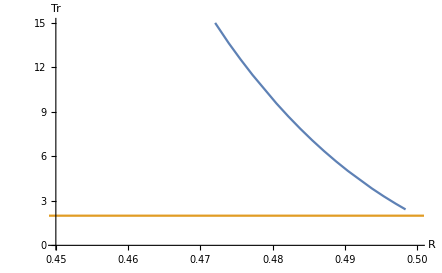

```mathematica
Plot[{%71,2},{R,0,5},PlotRange->{{0.45,0.5},{0,15}},AxesLabel->{HoldForm[R],HoldForm[Tr]}]
```

```mathematica
Export["C:\\Users\\ZanB\\Desktop\\TDS\\detelja.png",%93,"PNG"]
```

C:\Users\ZanB\Desktop\TDS\detelja.png

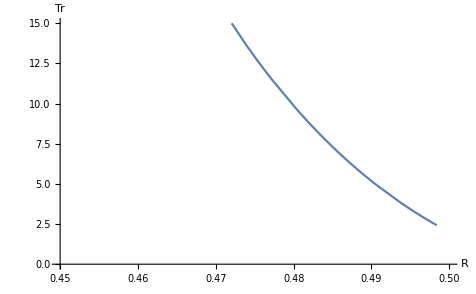

```mathematica
Show[%88,AxesLabel->{HoldForm[R],HoldForm[Tr]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

```mathematica
g[R_]:=1/R^4*2 *(6049 *R^4+32 *R^2 (125+32 √((-1+2 R)^2))-32 R^3 (244+105 √(R^2)+57 √((-1+2 R)^2))-256 R (4+√((-1+2 R)^2)+√(R^2) (3+8 √((-1+2 R)^2)))+64 (2+8 √(R^2) √((-1+2 R)^2)+3 (R^2)^(3/2) (16+15 √((-1+2 R)^2))))1/R^4 2 (6049 R^4+32 R^2 (125+32 √((-1+2 R)^2))-32 R^3 (244+105 √(R^2)+57 √((-1+2 R)^2))-256 R (4+√((-1+2 R)^2)+√(R^2) (3+8 √((-1+2 R)^2)))+64 (2+8 √(R^2) √((-1+2 R)^2)+3 (R^2)^(3/2) (16+15 √((-1+2 R)^2))));
Plot[g,{x,-5,50}]
```

-Graphics-